```mathematica
ClearAll["Global`*"];
ClearSystemCache[];
```

```mathematica
dir="C:\\Users\\werne\\Documents\\Thesis\\Modified_Keldysh_Latest\\Modified_Keldysh_Latest\\Output\\run3";
SetDirectory[dir];
```

```mathematica
λ={2.75,3.15,3.75,4.15};
```

```mathematica
edat={0.653750569,0.679630616,0.868601054,0.514673277}0.94/(200 10^-15)1/10^12;
r3={0.540017575, 0.517035313, 0.645093856, 0.440034927}0.94/(200 10^-15)1/10^12;
r2={0.288334046,0.293883741,0.330698184,0.21412698}0.94/(200 10^-15)1/10^12;
nir={{0.775,1.0673548387096772},{0.79,1.0846153846153845},{0.786,1.1336683417085425}};
```

```mathematica
th=Drop[Flatten[Import["thresholds.csv"]],1]*10^-16;
wl=Drop[Flatten[Import["wavelengths.csv"]],1]*10^6;
```

```mathematica
range={{2.5,4.5},{0,4}};
```

```mathematica
sim=Transpose[{wl,th}];
```

```mathematica
Needs["ErrorBarPlots`"];
ErDat[xdata_,ydata_,fraction_]:=Table[Append[{Transpose[{xdata,ydata}][[i]]},ErrorBar[fraction*ydata[[i]]]],{i,1,Length[ydata]}];
Plotter[errdata_,color_,legendtext_]:=ErrorListPlot[errdata,
ImageSize->500,
Axes->False,Frame->True,FrameStyle->Thick,TicksStyle->Thick,
FrameLabel->{{"Peak Intensity (TWcm^-2)",None},{"Wavelength (μm)",None}},
FrameTicks->Automatic,
BaseStyle->{FontSize->18,FontWeight->Bold,FontColor->Black},
LabelStyle->{FontSize->18,FontWeight->Bold,FontColor->Black},
PlotStyle->color,
PlotRange->range
]
```

```mathematica
regPlotter[errdata_,color_,legendtext_]:=ListPlot[errdata,
ImageSize->500,
Axes->False,Frame->True,FrameStyle->Thick,TicksStyle->Thick,
FrameLabel->{{"Peak Intensity (TWcm^-2)",None},{"Wavelength (μm)",None}},
FrameTicks->Automatic,
BaseStyle->{FontSize->18,FontWeight->Bold,FontColor->Black},
LabelStyle->{FontSize->18,FontWeight->Bold,FontColor->Black},
PlotStyle->color,
PlotRange->range
]
```

```mathematica
plotter[data_,color_,legendtext_]:=ListLinePlot[data,
ImageSize->500,
Axes->False,Frame->True,FrameStyle->Thick,TicksStyle->Thick,
FrameLabel->{{"Peak Intensity (TWcm^-2)",None},{"Wavelength (μm)",None}},
FrameTicks->Automatic,
BaseStyle->{FontSize->18,FontWeight->Bold,FontColor->Black},
LabelStyle->{FontSize->18,FontWeight->Bold,FontColor->Black},
PlotStyle->color,
PlotRange->range
]
```

```mathematica
r2dat=ErDat[λ,r2,0.1];
```

```mathematica
r2plot=Plotter[r2dat,Blue,"Region 2 (Melting)"];
nplot=regPlotter[nir,Darker[Green],""];
```

```mathematica
simplot=plotter[sim,Black,"Unmodified Gamaly"];
```

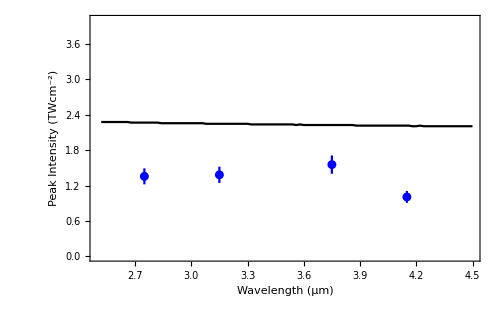

```mathematica
forexport=Show[nplot,simplot,r2plot,DataRange->{0,5}]
```

```mathematica
Export["TheoryData.PDF",forexport]
```

TheoryData.PDF

```mathematica
dir
```

C:\Users\werne\Documents\Thesis\Modified_Keldysh_Latest\Modified_Keldysh_Latest\Output\run3

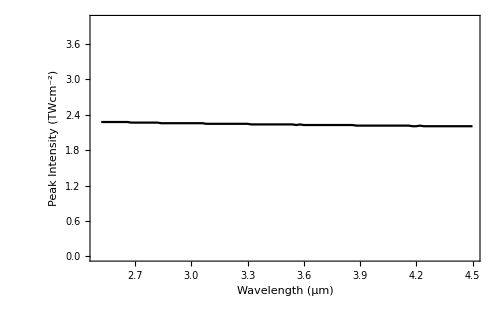

```mathematica
simplot
```

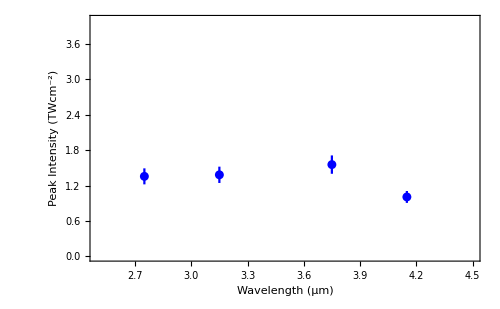

```mathematica
r2plot
```

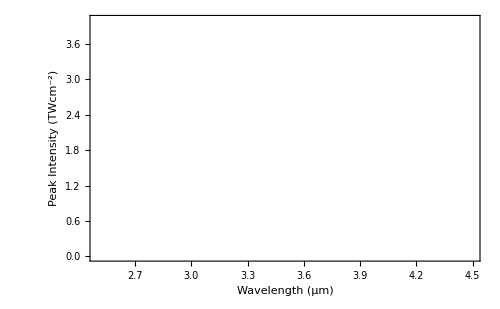

```mathematica
nplot
```

```mathematica
(*{775.,155.,0.176},{790.,130.,0.15},{786.,199.,0.24}*)
```

```mathematica
(*Allenspacher,Borowiec,Pronko*)
```

```mathematica
idx=Flatten[Position[sim[[All,1]],Nearest[sim[[All,1]],3.15][[1]]]][[1]];
sim[[idx]][[2]]
```

2.2448979591836732